# Quantum Random Walk: Naive Approach

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

The quantum random walker (Y. Aharonov, L. Davidovich, and N. Zagury "Quantum Random Walks" Phys. Rev. A 48, 1687 - 1690 (1993)) is made of a "coin" and a "walker", each one with its own state-space, which will make a composite system with the coin and the walker in entanglement. A unitary operator will be defined to "flip the coin", while another unitary operator will be defined to "move the walker" based on coin's result. The second operator produces entanglement between coin and walker.

## Load the Package

First load the Quantum`Notation` package. Write:
Needs["Quantum`Notation`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

In order to use the keyboard to enter quantum objects write:
SetQuantumAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQuantumAliases[];
```

## Quantum Random Walk in Dirac Notation

The coin C can have only two states, 0 and 1 (head and tail), while the walker P can be in any (integer) position. The coin is initially in state 0 and the wolker is initially at the origin 0:

```mathematica
|w[0]⟩=|Subscript[0, ĉ]⟩⊗|Subscript[0, p̂]⟩
```

|0_(ĉ),0_(p̂)⟩

Here we define the "flipping coin" operator, which in this case is a Hadamard operator, but it could be any unitary operator that acts only on the coin C. The coin have only two states, 0 and 1 (head and tail). Notice the last sign is negative:

```mathematica
h=1/(√2)(|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|+|Subscript[1, ĉ]⟩·⟨Subscript[0, ĉ]|+|Subscript[0, ĉ]⟩·⟨Subscript[1, ĉ]|-|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|)
```

(|0_(ĉ)⟩·⟨0_(ĉ)|+|1_(ĉ)⟩·⟨0_(ĉ)|+|0_(ĉ)⟩·⟨1_(ĉ)|-|1_(ĉ)⟩·⟨1_(ĉ)|)/(√2)

Here we define the "move the walker" operator. Its interpretation is very simple, the walkers P moves to the left j-1 if the coin is in state 0, and it moves to the right j+1 if the coin is in state 1. This is one of the "naive" parts of this implementation, it looks nice because it is exactly the same way you would do it by hand, but it is not computationally efficient to define the operator this way.

```mathematica
s=|Subscript[0, ĉ]⟩·⟨Subscript[0, ĉ]|⊗∑_(j=-∞)^∞ (|Subscript[(j-1), p̂]⟩·⟨Subscript[j, p̂]|)+
|Subscript[1, ĉ]⟩·⟨Subscript[1, ĉ]|⊗∑_(j=-∞)^∞ (|Subscript[(j+1), p̂]⟩·⟨Subscript[j, p̂]|)
```

∑_(j=-∞)^∞ |0_(ĉ),(-1+j)_(p̂)⟩·⟨0_(ĉ),j_(p̂)|+∑_(j=-∞)^∞ |1_(ĉ),(1+j)_(p̂)⟩·⟨1_(ĉ),j_(p̂)|

This is the evolution of the composite system of coin and walker: flip the coin with the operator h and then move the walker with operator s. The algebraic command Expand is necessary so that the calculation is performed and each intermidiate state is obtained as a linear superposition of basis states. This process is repeated "steps" times. This is a very naive implementation, therefore this evaluation can take several minutes in your computer. No output will be produced, however the evolution of the system is calculted and stored in |w[0]⟩,|w[1]⟩...|w[20]⟩

```mathematica
steps=20;
Do[|w[k]⟩=Expand[s·(h·|w[k-1]⟩)],
{k,1,steps}]
```

Each state of the composite system coin-walker is stored. For example this is the state at the third
step:

```mathematica
|w[3]⟩
```

(|0_(ĉ),(-3)_(p̂)⟩)/(2 √2)+(|0_(ĉ),(-1)_(p̂)⟩)/(√2)-(|0_(ĉ),1_(p̂)⟩)/(2 √2)+(|1_(ĉ),(-1)_(p̂)⟩)/(2 √2)+(|1_(ĉ),3_(p̂)⟩)/(2 √2)

And this is the state at the fifth state:

```mathematica
|w[5]⟩
```

(|0_(ĉ),(-5)_(p̂)⟩)/(4 √2)+(|0_(ĉ),(-3)_(p̂)⟩)/(√2)-(|0_(ĉ),3_(p̂)⟩)/(4 √2)+(|1_(ĉ),(-3)_(p̂)⟩)/(4 √2)+(|1_(ĉ),(-1)_(p̂)⟩)/(2 √2)-(|1_(ĉ),1_(p̂)⟩)/(2 √2)+(|1_(ĉ),3_(p̂)⟩)/(2 √2)+(|1_(ĉ),5_(p̂)⟩)/(4 √2)

Here we define the position projector for each position of the walker:

```mathematica
pp[j_]:=|Subscript[0, ĉ],Subscript[j, p̂]⟩·⟨Subscript[0, ĉ],Subscript[j, p̂]|+|Subscript[1, ĉ],Subscript[j, p̂]⟩·⟨Subscript[1, ĉ],Subscript[j, p̂]|
```

Here we calculate the probabilities for each walker position. This is another "naive" part of this implementation: It is not computationally efficient. This evaluation can take several seconds in your
computer:

```mathematica
probabilities=Table[{j,⟨w[steps]|·pp[j]·|w[steps]⟩},{j,-steps,steps}]
```

{{-20,1/1048576},{-19,0},{-18,181/524288},{-17,0},{-16,9257/524288},{-15,0},{-14,95617/524288},{-13,0},{-12,295265/1048576},{-11,0},{-10,965/32768},{-9,0},{-8,2501/32768},{-7,0},{-6,2377/32768},{-5,0},{-4,11221/262144},{-3,0},{-2,4165/131072},{-1,0},{0,3969/131072},{1,0},{2,3969/131072},{3,0},{4,7301/262144},{5,0},{6,637/32768},{7,0},{8,485/32768},{9,0},{10,1361/32768},{11,0},{12,28097/1048576},{13,0},{14,33317/524288},{15,0},{16,5417/524288},{17,0},{18,145/524288},{19,0},{20,1/1048576}}

Here is a plot of the probabilities for each position of the walker.

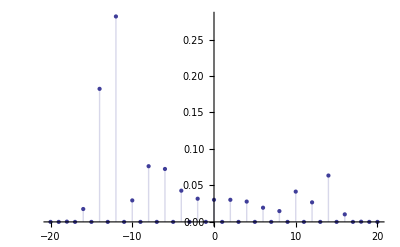

```mathematica
ListPlot[probabilities,PlotRange->All,Filling->Axis]
```

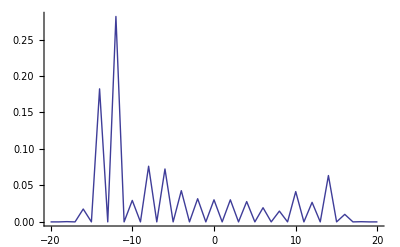

```mathematica
ListPlot[probabilities,PlotRange->All,Joined->True]
```

Another way to obtain the probabilities is using the Quantum Mathematica command QuantumMeasurement

```mathematica
qm= QuantumMeasurement[|w[steps]⟩,{p̂},FactorKet->False]
```

Probability | Measurement | State
1/1048576 | {{(-20)_(p̂)}} | |0_(ĉ),(-20)_(p̂)⟩
181/524288 | {{(-18)_(p̂)}} | (19 |0_(ĉ),(-18)_(p̂)⟩+|1_(ĉ),(-18)_(p̂)⟩)/(√362)
9257/524288 | {{(-16)_(p̂)}} | (135 |0_(ĉ),(-16)_(p̂)⟩+17 |1_(ĉ),(-16)_(p̂)⟩)/(√18514)
95617/524288 | {{(-14)_(p̂)}} | (425 |0_(ĉ),(-14)_(p̂)⟩+103 |1_(ĉ),(-14)_(p̂)⟩)/(√191234)
295265/1048576 | {{(-12)_(p̂)}} | (484 |0_(ĉ),(-12)_(p̂)⟩+247 |1_(ĉ),(-12)_(p̂)⟩)/(√295265)
965/32768 | {{(-10)_(p̂)}} | (-33 |0_(ĉ),(-10)_(p̂)⟩+29 |1_(ĉ),(-10)_(p̂)⟩)/(√1930)
2501/32768 | {{(-8)_(p̂)}} | -(49 |0_(ĉ),(-8)_(p̂)⟩+51 |1_(ĉ),(-8)_(p̂)⟩)/(√5002)
2377/32768 | {{(-6)_(p̂)}} | (65 |0_(ĉ),(-6)_(p̂)⟩+23 |1_(ĉ),(-6)_(p̂)⟩)/(√4754)
11221/262144 | {{(-4)_(p̂)}} | (-15 |0_(ĉ),(-4)_(p̂)⟩+2 |1_(ĉ),(-4)_(p̂)⟩)/(√229)
4165/131072 | {{(-2)_(p̂)}} | (11 |0_(ĉ),(-2)_(p̂)⟩-7 |1_(ĉ),(-2)_(p̂)⟩)/(√170)
3969/131072 | {{0_(p̂)}} | (-|0_(ĉ),0_(p̂)⟩+|1_(ĉ),0_(p̂)⟩)/(√2)
3969/131072 | {{2_(p̂)}} | (|0_(ĉ),2_(p̂)⟩-|1_(ĉ),2_(p̂)⟩)/(√2)
7301/262144 | {{4_(p̂)}} | (-10 |0_(ĉ),4_(p̂)⟩+7 |1_(ĉ),4_(p̂)⟩)/(√149)
637/32768 | {{6_(p̂)}} | (5 |0_(ĉ),6_(p̂)⟩-|1_(ĉ),6_(p̂)⟩)/(√26)
485/32768 | {{8_(p̂)}} | -(21 |0_(ĉ),8_(p̂)⟩+23 |1_(ĉ),8_(p̂)⟩)/(√970)
1361/32768 | {{10_(p̂)}} | (-11 |0_(ĉ),10_(p̂)⟩+51 |1_(ĉ),10_(p̂)⟩)/(√2722)
28097/1048576 | {{12_(p̂)}} | (121 |0_(ĉ),12_(p̂)⟩-116 |1_(ĉ),12_(p̂)⟩)/(√28097)
33317/524288 | {{14_(p̂)}} | (75 |0_(ĉ),14_(p̂)⟩-247 |1_(ĉ),14_(p̂)⟩)/(√66634)
5417/524288 | {{16_(p̂)}} | (15 |0_(ĉ),16_(p̂)⟩-103 |1_(ĉ),16_(p̂)⟩)/(√10834)
145/524288 | {{18_(p̂)}} | (|0_(ĉ),18_(p̂)⟩-17 |1_(ĉ),18_(p̂)⟩)/(√290)
1/1048576 | {{20_(p̂)}} | -|1_(ĉ),20_(p̂)⟩
Probability | Measurement | State

You can extract the list of probabilities using standard Mathematica notation. Remember that the measurement results were stored in the variable qm:

```mathematica
qm[[1,All,1]]
```

{1/1048576,181/524288,9257/524288,95617/524288,295265/1048576,965/32768,2501/32768,2377/32768,11221/262144,4165/131072,3969/131072,3969/131072,7301/262144,637/32768,485/32768,1361/32768,28097/1048576,33317/524288,5417/524288,145/524288,1/1048576}

The standard Mathematica command N[] gives the numerical values of the probabilities:

```mathematica
N[qm]
```

Probability | Measurement | State
9.53674×10^-7 | {{(-20)_(p̂)}} | |0_(ĉ),(-20)_(p̂)⟩
0.00034523 | {{(-18)_(p̂)}} | 0.0525588 (19. |0_(ĉ),(-18)_(p̂)⟩+|1_(ĉ),(-18)_(p̂)⟩)
0.0176563 | {{(-16)_(p̂)}} | 0.00734937 (135. |0_(ĉ),(-16)_(p̂)⟩+17. |1_(ĉ),(-16)_(p̂)⟩)
0.182375 | {{(-14)_(p̂)}} | 0.00228674 (425. |0_(ĉ),(-14)_(p̂)⟩+103. |1_(ĉ),(-14)_(p̂)⟩)
0.281587 | {{(-12)_(p̂)}} | 0.00184032 (484. |0_(ĉ),(-12)_(p̂)⟩+247. |1_(ĉ),(-12)_(p̂)⟩)
0.0294495 | {{(-10)_(p̂)}} | 0.0227626 (-33. |0_(ĉ),(-10)_(p̂)⟩+29. |1_(ĉ),(-10)_(p̂)⟩)
0.0763245 | {{(-8)_(p̂)}} | -0.0141393 (49. |0_(ĉ),(-8)_(p̂)⟩+51. |1_(ĉ),(-8)_(p̂)⟩)
0.0725403 | {{(-6)_(p̂)}} | 0.0145034 (65. |0_(ĉ),(-6)_(p̂)⟩+23. |1_(ĉ),(-6)_(p̂)⟩)
0.0428047 | {{(-4)_(p̂)}} | 0.0660819 (-15. |0_(ĉ),(-4)_(p̂)⟩+2. |1_(ĉ),(-4)_(p̂)⟩)
0.0317764 | {{(-2)_(p̂)}} | 0.0766965 (11. |0_(ĉ),(-2)_(p̂)⟩-7. |1_(ĉ),(-2)_(p̂)⟩)
0.0302811 | {{0_(p̂)}} | 0.707107 (-1. |0_(ĉ),0_(p̂)⟩+|1_(ĉ),0_(p̂)⟩)
0.0302811 | {{2_(p̂)}} | 0.707107 (|0_(ĉ),2_(p̂)⟩-1. |1_(ĉ),2_(p̂)⟩)
0.0278511 | {{4_(p̂)}} | 0.0819232 (-10. |0_(ĉ),4_(p̂)⟩+7. |1_(ĉ),4_(p̂)⟩)
0.0194397 | {{6_(p̂)}} | 0.196116 (5. |0_(ĉ),6_(p̂)⟩-1. |1_(ĉ),6_(p̂)⟩)
0.014801 | {{8_(p̂)}} | -0.0321081 (21. |0_(ĉ),8_(p̂)⟩+23. |1_(ĉ),8_(p̂)⟩)
0.0415344 | {{10_(p̂)}} | 0.0191671 (-11. |0_(ĉ),10_(p̂)⟩+51. |1_(ĉ),10_(p̂)⟩)
0.0267954 | {{12_(p̂)}} | 0.00596582 (121. |0_(ĉ),12_(p̂)⟩-116. |1_(ĉ),12_(p̂)⟩)
0.0635471 | {{14_(p̂)}} | 0.00387393 (75. |0_(ĉ),14_(p̂)⟩-247. |1_(ĉ),14_(p̂)⟩)
0.0103321 | {{16_(p̂)}} | 0.00960739 (15. |0_(ĉ),16_(p̂)⟩-103. |1_(ĉ),16_(p̂)⟩)
0.000276566 | {{18_(p̂)}} | 0.058722 (|0_(ĉ),18_(p̂)⟩-17. |1_(ĉ),18_(p̂)⟩)
9.53674×10^-7 | {{20_(p̂)}} | -1. |1_(ĉ),20_(p̂)⟩
Probability | Measurement | State

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx